# Cos Vs Gauss Tunneling

### Numbers:

```mathematica
ℏ=1.05457*10^-34;
λ=852.0*10^-9;
ks=(2π)/λ; (*wavevector for the short lattice*)
kl=π/λ; (*wavevector for the long lattice*)
a=λ/2;  (*short lattice spacing*)
amu=1.6605*10^-27;
mRb=86.909*amu;  (*mass or Rb87*)
Er=(ℏ^2 ks^2)/(2mRb); (*Recoil energy of the short lattice*)
as=5.3*10^-9;   (*approximate s-wave scattering length for Rb87 (in meters)*)
```

```mathematica
λ=852.0*10^-9;
ks=(2π)/λ;
Er=N[(ℏ^2 ks^2)/(2mRb)];

btwn=.9*10^-6;
waist=.75*10^-6;
```

```mathematica
Vt=Er/(ℏ^2/(mRb*waist^2))//N
```

15.2958

### Density Plot

15.2958

```mathematica
(*First, show how the tunneling rates of the sinusoid depend on things*)
```

```mathematica
DensityPlot[Log10[SinTunnel[V,λ]],{V,0,25},{λ,.2*10^-6,.9*10^-6},PlotLegends->Automatic,PlotPoints->66]
```

-Graphics-

One can use the function SinTunnel to plot the cos tunneling rates in the following way:

```mathematica
(*Plot[SinTunnel[V (in units of Er), λ (in SI units)]]*)
```

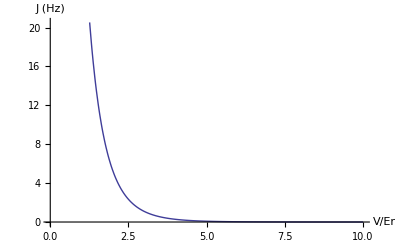

```mathematica
Plot[SinTunnel[V,.9*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
```

```mathematica
Plot[SinTunnel[V,.9*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
Plot[SinTunnel[V,.85*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
Plot[SinTunnel[V,.6*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
Plot[SinTunnel[V,.4*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
Plot[SinTunnel[V,.3*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
Plot[SinTunnel[V,.2*10^-6],{V,0,10},AxesLabel->{"V/Er","J (Hz)"}]
```

```mathematica
(*I hope this is what you wanted, Cindy. Here are some plots that will show you the tunneling rates for different values of b.*)
```

```mathematica
Additionally, I can try to fit this to the cos as discussed in the group meeting
```

First, I define a function that will find the bump height of the well, as well as define a function that is my gaussian potential:

## Fitting Sins to Gaussians

```mathematica
F[x_,V_,b_]:=-V*Vt*Exp[-2*(x-b)^2]-V*Vt*Exp[-2*(x+b)^2]
```

```mathematica
Vscale[b_]:=Module[{x},
F[x_]:=-Exp[-2*(x-b)^2]-Exp[-2*(x+b)^2];
V =F[0]-FindMinimum[F[x],{x,1.1}][[1]]
]
```

Now, I will test it out.

```mathematica
Vscale[1.1]
```

0.822219

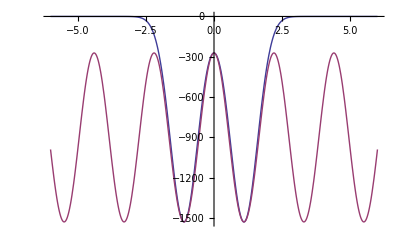

```mathematica
V0=0.8222193244670273;
Plot[{F[x,100,1.1],(F[0,100,1.1]+Vscale[1.1]*Vt*100/2*(-1+Cos[2*π/(2*1.1)*x]))},{x,-6,6}]
```

```mathematica
(*This is working well, up to an energy constant offset that we can ignore. Now, we can use this to plot tunneling rates*)
```

## Tunneling Rates:

```mathematica
b=.9*10^-6 m
```

```mathematica
b=.9*10^-6
```

9.×10^-7

```mathematica
bscale=b/waist
```

1.2

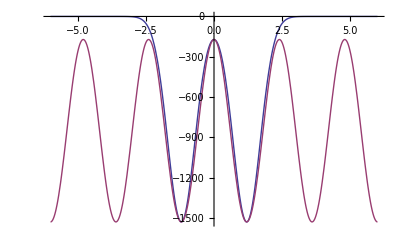

```mathematica
Plot[{F[x,100,bscale],(F[0,100,bscale]+Vscale[bscale]*Vt*100/2*(-1+Cos[2*π/(2*bscale)*x]))},{x,-6,6}]
```

First, calculate the tunneling rates of the sin potential:

```mathematica
V0=Vscale[bscale]
```

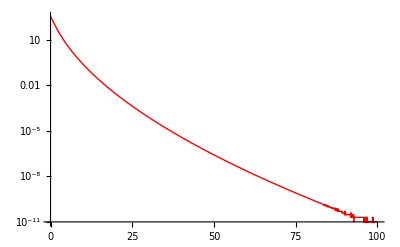

```mathematica
psin=LogPlot[SinTunnel[-V0*V,b],{V,0,100},PlotStyle->Red]
```

We can compare this to the 1D calculate tunneling rates for the gaussian well:

```mathematica
gaustunb1= Table[{V,(computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b/waist)/2.,12,100][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b/waist)/2.,12,100][[1]][[1]])*scalin/2},{V,0,100,5}]
```

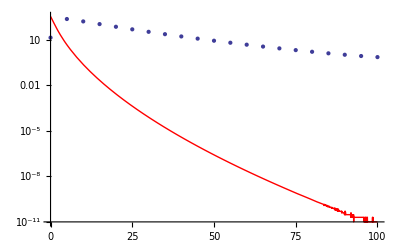

```mathematica
Show[psin,ListLogPlot[gaustunb1]]
```

```mathematica
(*A little nicer plot*)
```

```mathematica
sintunb1 = Table[{V,SinTunnel[V*V0,b]},{V,0,100,5}]
```

{{0,353.572},{5,4.79763},{10,0.241086},{15,0.0218008},{20,0.00274885},{25,0.000432642},{30,0.0000800489},{35,0.0000167808},{40,3.88871×10^-6},{45,9.78972×10^-7},{50,2.64313×10^-7},{55,7.57862×10^-8},{60,2.28975×10^-8},{65,7.24482×10^-9},{70,2.38641×10^-9},{75,8.15609×10^-10},{80,2.92008×10^-10},{85,1.00692×10^-10},{90,4.0277×10^-11},{95,1.00692×10^-11},{100,1.00692×10^-11}}

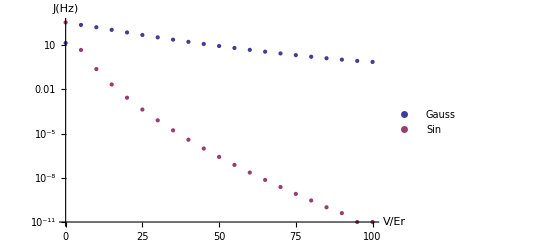

```mathematica
ListLogPlot[{gaustunb1,sintunb1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
```

## b ==.65*10^-6

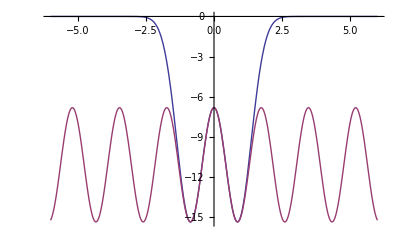

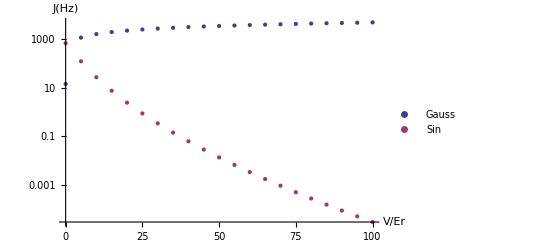

```mathematica
b=.65*10^-6(*enter value for b in si*)
p=100(*Number of basis states. Rough: 100 is fine up to around V/Er =100, depending on waist. For V/Er =700, you need 300 basis states*)
bscale=b/waist
Plot[{F[x,1,bscale],(F[0,1,bscale]+Vscale[bscale]*Vt*1/2*(-1+Cos[2*π/(2*bscale)*x]))},{x,-6,6}]
gaustunu1= Table[{V,(computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,12,p][[1]][[2]]-computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,12,p][[1]][[1]])*scalin/2},{V,0,p,5}]
V0=Vscale[bscale]
sintunbu1 = Table[{V,SinTunnel[V*V0,b]},{V,0,100,5}]
ListLogPlot[{gaustunu1,sintunbu1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
```

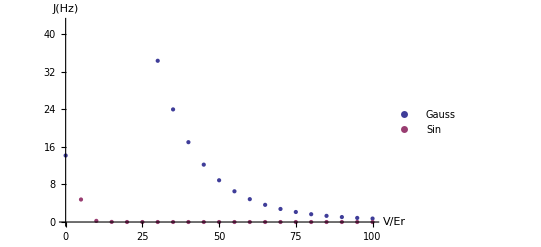

```mathematica
ListPlot[{gaustunb1,sintunb1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
```

## TEMPLATE

```mathematica
(*Note on scale factors. Adam's code is written with the recoil energy as the scaling factor, Er. Due to a different path I took, my scale factor looks like Vt=ℏ^2/(mRb*waist^2). So, whenever you see an Er/Vt, I am simply converting between scale factors. The ratio is about 15 if you are curious. So, when Adam puts a well depth of 100 Er, that corresponds to about 1500 Vt units. The code that I wrote needs things in units of Vt, which is why it is converted.
```

```mathematica
b=(*enter value for b in si*)
p=(*Number of basis states. Rough: 100 is fine up to around V =100 Vt, depending on waist. For V =700 Vt, you need 300 basis states. Converting into recoils, for V = 46 Er, you need 300 basis states, and higher, depending on the b you are working with. The tunneling rates will start to curve up when it stops converging*)
bscale=b/waist
Plot[{F[x,1,bscale],(F[0,1,bscale]+Vscale[bscale]*Vt*100/2*(-1+Cos[2*π/(2*bscale)*x]))},{x,-6,6}]
gaustunu1= Table[{V,(computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,12,p][[1]][[2]]-computePlaneMatrix2Well[Vt*V,.5,(b/waist)/2.,12,][[1]][[1]])*scalin/2},{V,0,p,5}]
V0=Vscale[bscale]
sintunbu1 = Table[{V,SinTunnel[V*V0,b]},{V,0,100,5}]
ListLogPlot[{gaustunb1,sintunb1},PlotLegends->{"Gauss","Sin"},AxesLabel->{"V/Er","J(Hz)"}]
```

## Functions:

```mathematica
Clear[h]
Clear[M]
h = 1.05457173*10^-34;
M = 1.443161*10^-25;
```

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Compile[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

0.0103913

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Compile[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

(1-size)/2+(i-Mod[i,size,1])/size

```mathematica
kx[6,5]
```

-1

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2WellH[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]

]
```

```mathematica
computePlaneMatrix2WellBox[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - 1/2(V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[1/(2 c^2)(-b+ⅈ*c^2(m-l))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length)-1/2(V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[(1/(2 c^2)(b+ⅈ*c^2(m-l))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length);
M = Eigensystem[Table[H[π*l/length,π*m/length],{l,1,p},{m,1,p}]-10000*IdentityMatrix[p],3]

]
```

```mathematica
ComputePlaneWaveEN[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigenvalues[M-10000*IdentityMatrix[p^2],3]
]
```

```mathematica
(-bsep+ⅈ*c^2(l-m))^2//Expand
```

bsep^2-2 ⅈ bsep c^2 l-c^4 l^2+2 ⅈ bsep c^2 m+2 c^4 l m-c^4 m^2

```mathematica
1/2 (k-l) (2 ⅈ bsep+(-k+l) w^2)//Expand
```

ⅈ bsep k-ⅈ bsep l-(k^2 w^2)/2+k l w^2-(l^2 w^2)/2

```mathematica
Tunneling2D[V_,L_,p_,b_]:= Module[{En0,En1, EnList,T},
EnList = Eigenvalues[BuildPlaneMatrix2D2Well[V,L,p,b/2.]-1000.*IdentityMatrix[p^2],2]+1000;
En1 = EnList[[2]];
En0  =EnList [[1]];
T = En1-En0
]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*Compute eigenvalues for the gaussian well. Note, for all the work I am doing c=.5, this is because the experimentalists, work with a Exp[-2()^2/c^2], where I defined my c Exp[-()^2/(2*c^2)]. Since I work in units of the waist, c=1, but, by putting it c=.5, I get to pop out the 2 on the top.*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

```mathematica
SinTunnel[VEr_,λsi_]:=Module[{Et,Er},
(*The mathieucharateristic function will give the value 'a', corresponding to the equation:
y'' +(a+2*q*Cos[2*z])y = 0. So, one has to get the SWE into a form like this. This is why the Et factor comes in:
h^2/(2*m)d^2 ψ^2/dx^2+V/2*Cos[2*π/λ*x]-E=0 -> d^2 ψ^2/dθ^2+V/2(2*m/(ℏ^2 χ^2))Cos[2*π/λ*χ*θ]-E=0
where χ contains the units and scaling of x. To get the Cos term to look right, this becomes: χ=λ/π, and the equation becomes:
d^2 ψ^2/dθ^2+2(V/4(2*(m*λ^2)/(ℏ^2*π^2)))Cos[2θ]-E*(2*(m*λ^2)/(ℏ^2*π^2))=0, so the term in brackets is the scaling factor Et*)


Er=(ℏ^2 ks^2)/(2mRb);
Et =π^2*ℏ^2/(2*mRb*(λsi)^2);
1/2(MathieuCharacteristicA[.999,(VEr*Er*1/(4Et))]-MathieuCharacteristicA[0,(VEr*Er*1/(4Et))])*Et/(2*π*ℏ)
]
```